```mathematica
g=0.2;
m=0.318*g;
κ=Exp[EulerGamma]m/g;
M=g/Sqrt[Pi];
```

```mathematica
Φvac=0;
Mp2=M^2(1+2Sqrt[Pi]κ Cos[2Sqrt[Pi]Φvac]);
inhom=M^2 ((2Sqrt[Pi]Φvac+2Pi)Cos[2Sqrt[Pi]Φvac]-M^2 κ Sin[2Sqrt[Pi]Φvac]);
```

```mathematica
τ0=0.01;
ϕ0=inhom/Mp2+(Φvac+Sqrt[Pi]-inhom/Mp2)BesselJ[0,Sqrt[Mp2]τ0];
ϕ0p=-Sqrt[Mp2](Φvac+Sqrt[Pi]-inhom/Mp2)BesselJ[1,Sqrt[Mp2]τ0];
```

```mathematica
sol=NDSolve[{ϕ''[τ]+1/τ ϕ'[τ]+M^2(ϕ[τ]+κ Sin[2 Sqrt[Pi] ϕ[τ]])==0,ϕ[τ0]==ϕ0,ϕ'[τ0]==ϕ0p},ϕ[τ],{τ,τ0,50}]
```

{{ϕ[τ]→InterpolatingFunction[{{0.01, 50.}}, <>][τ]}}

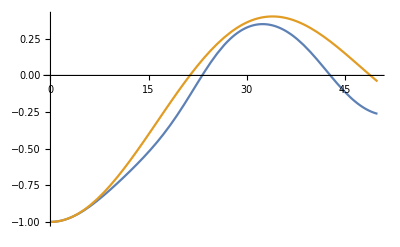

```mathematica
Plot[{-ϕ[τ]/Sqrt[Pi]/. sol,-BesselJ[0,M τ]},{τ,τ0,50}]
```

```mathematica
tabphi=Table[{τ,(-ϕ[τ]/Sqrt[Pi]/. sol)[[1]]},{τ,τ0,50,0.1}];
```

```mathematica
(* Export["tabphi_2.dat",tabphi]*)
```